Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

2 - 11 Cauchy-Riemann equations
Are the following functions analytic? Use (1) on p. 625 or (7) on p. 628.

3.  f[z]=ⅇ^(-2 x)(Cos[2 y]-ⅈ Sin[2 y])

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_]=ⅇ^(-2 x)(Cos[2 y]-ⅈ Sin[2 y])
```

ⅇ^(-2 x) (Cos[2 y]-ⅈ Sin[2 y])

The test for analyticity for complex functions comes from the Cauchy-Riemann criterion.

```mathematica
u[x_,y_]=ⅇ^(-2 x)Cos[2 y]
```

ⅇ^(-2 x) Cos[2 y]

```mathematica
v[x_,y_]=-ⅇ^(-2 x) Sin[2 y]
```

-ⅇ^(-2 x) Sin[2 y]

```mathematica
PossibleZeroQ[D[u[x,y],x]-D[v[x,y],y]]
PossibleZeroQ[D[v[x,y],x]+D[u[x,y],y]]
```

True

True

The function f passes the C-R test and is therefore analytic, yes.

5.  f[z]=Re[z^2]-ⅈ Im[z^2]

```mathematica
Clear["Global`*"]
```

```mathematica
z=x + ⅈ y
```

x+ⅈ y

```mathematica
f[x_,y_]=Re[z^2]-ⅈ Im[z^2]
```

-ⅈ Im[(x+ⅈ y)^2]+Re[(x+ⅈ y)^2]

```mathematica
ComplexExpand[f[x,y]]
```

x^2-2 ⅈ x y-y^2

```mathematica
u[x_,y_]=x^2-y^2
```

x^2-y^2

```mathematica
v[x_,y_]=-2  x y
```

-2 x y

```mathematica
PossibleZeroQ[D[u[x,y],x]-D[v[x,y],y]]
PossibleZeroQ[D[v[x,y],x]+D[u[x,y],y]]
```

False

False

PZQs are not both true in this case, therefore f is not analytic, no.

7.  f[z]=ⅈ/z^8

```mathematica
Clear["Global`*"]
```

```mathematica
z=x + ⅈ y
```

x+ⅈ y

```mathematica
f[x_,y_]=ⅈ/z^8
```

ⅈ/(x+ⅈ y)^8

```mathematica
ComplexExpand[f[x,y]]
```

(8 x^7 y)/((x^2+y^2)^8)-(56 x^5 y^3)/((x^2+y^2)^8)+(56 x^3 y^5)/((x^2+y^2)^8)-(8 x y^7)/((x^2+y^2)^8)+ⅈ (x^8/((x^2+y^2)^8)-(28 x^6 y^2)/((x^2+y^2)^8)+(70 x^4 y^4)/((x^2+y^2)^8)-(28 x^2 y^6)/((x^2+y^2)^8)+y^8/((x^2+y^2)^8))

```mathematica
u[x_,y_]=(8 x^7 y)/((x^2+y^2)^8)-(56 x^5 y^3)/((x^2+y^2)^8)+(56 x^3 y^5)/((x^2+y^2)^8)-(8 x y^7)/((x^2+y^2)^8);
```

```mathematica
v[x_,y_]=x^8/((x^2+y^2)^8)-(28 x^6 y^2)/((x^2+y^2)^8)+(70 x^4 y^4)/((x^2+y^2)^8)-(28 x^2 y^6)/((x^2+y^2)^8)+y^8/((x^2+y^2)^8);
```

```mathematica
PossibleZeroQ[D[u[x,y],x]-D[v[x,y],y]]
PossibleZeroQ[D[v[x,y],x]+D[u[x,y],y]]
```

True

True

From the problem description in can be seen that z cannot be 0; otherwise, since PZQs are both true, the expression f[z] is analytic, yes.

9.  f[z]=(3 π^2)/(z^3+4 π^2 z)

```mathematica
Clear["Global`*"]
```

```mathematica
f[z]=(3 π^2)/(z^3+4 π^2 z)
```

(3 π^2)/(4 π^2 z+z^3)

```mathematica
ff[x_,y_]=f[z]/.z->x+ⅈ y
```

(3 π^2)/(4 π^2 (x+ⅈ y)+(x+ⅈ y)^3)

```mathematica
dr=ComplexExpand[Re[ff[x,y]]];
```

```mathematica
u[x_,y_]=FullSimplify[dr]
```

(3 π^2 x (4 π^2+x^2-3 y^2))/((x^2+y^2) (16 π^4+8 π^2 (x-y) (x+y)+(x^2+y^2)^2))

```mathematica
di=ComplexExpand[Im[ff[x,y]]];
```

```mathematica
v[x_,y_]=FullSimplify[di]
```

(3 π^2 y (-4 π^2-3 x^2+y^2))/((x^2+y^2) (16 π^4+8 π^2 (x-y) (x+y)+(x^2+y^2)^2))

```mathematica
PossibleZeroQ[D[u[x,y],x]-D[v[x,y],y]]
PossibleZeroQ[D[v[x,y],x]+D[u[x,y],y]]
```

True

True

Here is another case where z is not allowed to equal zero; with that exception, PZQs are both true, so the function is judged analytic, yes.

11.  f[z] = Cos[x] Cosh[y] - I Sin[x] Sinh[y]

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_,y_] = Cos[x] Cosh[y] - I Sin[x] Sinh[y]
```

Cos[x] Cosh[y]-ⅈ Sin[x] Sinh[y]

```mathematica
f[z]=Cos[x] Cosh[y]-I Sin[x] Sinh[y]
```

Cos[x] Cosh[y]-ⅈ Sin[x] Sinh[y]

```mathematica
u[x_,y_]=Cos[x] Cosh[y]
```

Cos[x] Cosh[y]

```mathematica
v[x_,y_]=-Sin[x] Sinh[y]
```

-Sin[x] Sinh[y]

```mathematica
PossibleZeroQ[D[u[x,y],x]-D[v[x,y],y]]
PossibleZeroQ[D[v[x,y],x]+D[u[x,y],y]]
```

True

True

In this case there are no domain restrictions, and the Cauchy-Riemann test is passed by u and v, yes.

Are the following functions harmonic? If your answer is yes, find a corresponding analytic function f[z]=u[x,y]+ⅈv[x,y].

13.  u = x y

```mathematica
Clear["Global`*"]
```

```mathematica
u[x_,y_]=x y
```

x y

```mathematica
Simplify[Laplacian[u[x,y],{x,y}]]
```

0

The function u passes the test for harmonic function. Now to look for a corresponding analytic function.

```mathematica
D[u[x,y],x]
```

y

v_y=u_x=y   and   v_x=-u_y=-x

according to the Cauchy-Riemann criteria, which I must follow. Integrating the first equation with respect to y and differentiating the result with respect to x, I get

v=1/2 y^2+h[x]  and   v_x= dh/dx

A comparison with the last v_x with the expressions in the yellow cell shows that dh/dx=-x   or  h[x]=-1/2 x^2

Thus the following results:

```mathematica
f[z]=u +ⅈ v=x y+ⅈ(1/2 y^2+-1/2 x^2+C)
```

Set::write: Tag Plus in u+ⅈ v is Protected.

x y+ⅈ (C-x^2/2+y^2/2)

```mathematica
out=Simplify[x y+ⅈ(1/2 y^2+-1/2 x^2+C)]
```

ⅈ C-1/2 ⅈ (x+ⅈ y)^2

```mathematica
out1=out/.(x+ⅈ y)->z
```

ⅈ C-(ⅈ z^2)/2

```mathematica
Solve[-1/2 ⅈ(z^2+c)==ⅈ C-(ⅈ z^2)/2,C]
```

{{C→-c/2}}

The green cell above matches the text answer, modified by the value of C (real) shown in the purple cell.

15.  u=x/(x^2+y^2)

```mathematica
Clear["Global`*"]
```

```mathematica
u[x_,y_]=x/(x^2+y^2)
```

x/(x^2+y^2)

```mathematica
Simplify[Laplacian[u[x,y],{x,y}]]
```

0

The function u passes the test for harmonic function. Now to look for a corresponding analytic function.

```mathematica
D[u[x,y],x]
```

-(2 x^2)/((x^2+y^2)^2)+1/(x^2+y^2)

```mathematica
-D[u[x,y],y]
```

(2 x y)/((x^2+y^2)^2)

v_y=u_x=-(2 x^2)/((x^2+y^2)^2)+1/(x^2+y^2)   and   v_x=-u_y=(2 x y)/((x^2+y^2)^2)

Integrating the first equation with respect to y and differentiating the result with respect to x, I get

```mathematica
vup=∫(-(2 x^2)/((x^2+y^2)^2)+1/(x^2+y^2))ⅆy
```

-y/(x^2+y^2)

```mathematica
vup2=vup +h[x]+C
```

C-y/(x^2+y^2)+h[x]

```mathematica
Subscript[v, x]=D[vup2,x]
```

(2 x y)/((x^2+y^2)^2)+h'[x]

A comparison with the expressions in the yellow cell shows that dh/dx=0   or  h[x]=C1. 
Thus  f[z] = u[x, y] + ⅈ v[x, y] and (making C2=C+C1)

```mathematica
f[z]=x/(x^2+y^2) +ⅈ(-y/(x^2+y^2)+C2)
```

x/(x^2+y^2)+ⅈ (C2-y/(x^2+y^2))

```mathematica
f1[z]=Simplify[f[z]]
```

(1+ⅈ C2 x-C2 y)/(x+ⅈ y)

```mathematica
f2[z]=f1[z]/.(x+ⅈ y)->z
```

(1+ⅈ C2 x-C2 y)/z

```mathematica
f3[z]=(1+ⅈ C2 (x  + ⅈ y))/z==(1+ⅈ C2 z)/z==1/z+ⅈ C2;
```

This answer does not match the text because a real constant C is left sitting next to an imaginary unit. Since the text answer is 1/z+C, C real, I think it would be an abuse to show green here. Or maybe not. If C is is chosen as 0, then the answer can be green.

17.  v = (2 x + 1) y

This one has the twist of looking for u instead of the usual v.

```mathematica
Clear["Global`*"]
```

```mathematica
v[x_,y_]=(2 x+1) y
```

(1+2 x) y

```mathematica
Simplify[Laplacian[v[x,y],{x,y}]]
```

0

The function v passes the test for harmonic function. Now to look for a corresponding analytic function.

```mathematica
-D[v[x,y],x]
```

-2 y

```mathematica
D[v[x,y],y]
```

1+2 x

u_x=v_y=1+2 x   and   u_y=-v_x=-2 y

Integrating the first equation with respect to x and differentiating the result with respect to y, I get

```mathematica
up=∫(1+2 x) ⅆx
```

x+x^2

```mathematica
up2=up +h[y]+c
```

c+x+x^2+h[y]

```mathematica
Subscript[u, y]=D[up2,y]
```

h'[y]

A comparison with the expressions in the yellow cell shows that dh/dy=-2 y   or  h[y]=-y^2.  Thus

f[z] = u[x, y] + ⅈ v[x, y] and

```mathematica
f[z]=x+x^2+c-y^2 +ⅈ((2 x+1) y)
```

c+x+x^2+ⅈ (1+2 x) y-y^2

```mathematica
f1[z]=FullSimplify[f[z]]
```

c+(x+ⅈ y) (1+x+ⅈ y)

```mathematica
f2[z]=f1[z]/.(x+ⅈ y)->z
```

c+z (1+z)

19.  v=ⅇ^x Sin[2 y]

Again my quarry is the u function instead of the v function.

```mathematica
Clear["Global`*"]
```

```mathematica
v[x_,y_]=ⅇ^x Sin[2 y]
```

ⅇ^x Sin[2 y]

```mathematica
Simplify[Laplacian[v[x,y],{x,y}]]
```

-3 ⅇ^x Sin[2 y]

The green cell above is not 0; therefore the function is not harmonic.

21 - 24 Determine a and b so that the given function is harmonic and find a harmonic conjugate.

21.  u=ⅇ^(π x)Cos[a v]

This looks pretty intimidating as written; I’m going to start by assuming a typo, and insert y for v.

```mathematica
Clear["Global`*"]
```

```mathematica
u[x_,y_]=ⅇ^(π x)Cos[π y]
```

ⅇ^(π x) Cos[π y]

```mathematica
Simplify[Laplacian[u[x,y],{x,y}]]
```

0

It looks like a needs to equal π in order to have a harmonic function.

```mathematica
D[u[x,y],x]
```

ⅇ^(π x) π Cos[π y]

```mathematica
-D[u[x,y],y]
```

ⅇ^(π x) π Sin[π y]

v_y=u_x=ⅇ^(π x) π Cos[π y]   and   v_x=-u_y=ⅇ^(π x) π Sin[π y]

Integrating the first equation with respect to y and differentiating the result with respect to x, I get

```mathematica
vup=∫(ⅇ^(π x) π Cos[π y])ⅆy
```

ⅇ^(π x) Sin[π y]

As usual Mathematica neglects to insert a constant of integration. However, in this case the omission lands on the text answer.

```mathematica
vup2=vup +h[x]
```

h[x]+ⅇ^(π x) Sin[π y]

```mathematica
Subscript[v, x]=D[vup2,x]
```

ⅇ^(π x) π Sin[π y]+h'[x]

A comparison of v_x with the expressions in the yellow cell shows that dh/dx=0   or  h[x]=C. 
Thus  f[z] = u[x, y] + ⅈ v[x, y] and

```mathematica
f[z]=ⅇ^(π x)Cos[π y]+ⅈ (ⅇ^(π x) Sin[π y]+c)
```

ⅇ^(π x) Cos[π y]+ⅈ (c+ⅇ^(π x) Sin[π y])

The green cell above agrees with the text answer for v[x,y]. However, for f[z], I believe a constant has to come in there. Unless I was wrong about the typo, and (due to principles not understood by me) that accounts for the text dispensing with the constant.

23.  u=a x^3+b x y

```mathematica
Clear["Global`*"]
```

```mathematica
u[x_,y_]=a x^3+b x y
```

a x^3+b x y

```mathematica
Simplify[Laplacian[u[x,y],{x,y}]]
```

6 a x

It appears that a must equal zero for the function to be harmonic.

```mathematica
u[x_,y_]=b x y
```

b x y

```mathematica
Simplify[Laplacian[u[x,y],{x,y}]]
```

0

```mathematica
D[u[x,y],x]
```

b y

```mathematica
-D[u[x,y],y]
```

-b x

v_y=u_x=b y   and   v_x=-u_y=-b x

Integrating the first equation with respect to y and differentiating the result with respect to x, I get

```mathematica
vup=∫b yⅆy
```

(b y^2)/2

```mathematica
vup2=vup +h[x]+c
```

c+(b y^2)/2+h[x]

```mathematica
Subscript[v, x]=D[vup2,x]
```

h'[x]

A comparison with the expressions in the yellow cell shows that dh/dx=-b x   or  h[x]=-b/2 x^2. 
Thus  f[z] = u[x, y] + ⅈ v[x, y] and

```mathematica
f[z]=b x y+ⅈ[(b y^2)/2-(b x^2)/2+c]
```

b x y+ⅈ[c-(b x^2)/2+(b y^2)/2]

```mathematica
f1[z]=Simplify[f[z]]
```

b x y+ⅈ[c+1/2 b (-x^2+y^2)]

The green cell matches the text answer. I noticed this when I saw that only v is covered in the answer, not f[z].

25. CAS Project. Equipotential Lines. Write a program for graphing equipotential lines u=const of a harmonic function u and of its conjugate v on the same axes. Apply the program to (a) u=x^2-y^2, v=2 x y, (b) u=x^3-3 x^2 y-y^3, v=3 x^2 y-y^3.

Part (a)

In a spooky coincidence, the exact same equations for part (a) were the subject of discussion in Mathematica StackExchange question #153214.

```mathematica
cp1=ContourPlot[x^2-y^2,{x,-10,10},{y,-10,10},Contours->20,PlotLegends->Automatic,ColorFunction->"Rainbow",ContourStyle->Blue,Epilog->{{Red,Arrowheads[.03],Arrow[{{-4,11},{-4,4}}]},{Text["harmonic component",{-4,7}]},{Red,Arrowheads[.03],Arrow[{{-1,11},{-1,0}}]},{Text["conjugate component",{-0.6,2.3}]}}];
```

```mathematica
cp2=ContourPlot[2 x y,{x,-10,10},{y,-10,10},Mesh->None,(*ContourShading->None,*)ColorFunction->Function[f,Opacity[.5,ColorData["Rainbow"][f]]],Contours->20,PlotLegends->Automatic];
```

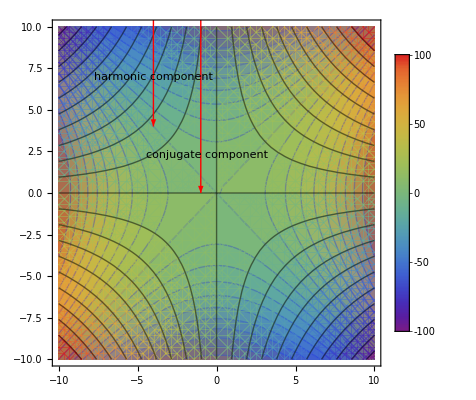

```mathematica
Show[cp1,cp2/.EdgeForm[]->EdgeForm[Opacity[0]]]
```

Part (b)

```mathematica
Clear["Global`*"]
```

```mathematica
cp1=ContourPlot[x^3-3 x^2 y-y^3,{x,-10,10},{y,-10,10},Contours->20,PlotLegends->Automatic,ColorFunction->"Rainbow",ContourStyle->Blue,Epilog->{{Red,Arrowheads[.03],Arrow[{{-4,11},{-4,5.3}}]},{Text["harmonic component",{-4,7}]},{Red,Arrowheads[.03],Arrow[{{0,11},{0,5.75}}]},{Text["conjugate component",{0,9}]}}];
```

```mathematica
cp2=ContourPlot[3 x^2 y-y^3,{x,-10,10},{y,-10,10},Mesh->None,(*ContourShading->None,*)ColorFunction->Function[f,Opacity[.5,ColorData["Rainbow"][f]]],Contours->20,PlotLegends->Automatic];
```

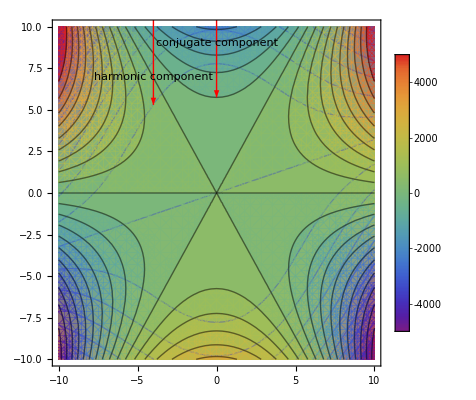

```mathematica
Show[cp1,cp2/.EdgeForm[]->EdgeForm[Opacity[0]]]
```